```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
outMbdf2 = ReadList["outMbdf2.txt", {Number,Number, Number}];
y1outMbdf2 = ReadList["./y1/outMbdf2.txt", {Number,Number}];
y2outMbdf2 = ReadList["./y2/outMbdf2.txt", {Number,Number}];
y3outMbdf2 = ReadList["./y3/outMbdf2.txt", {Number,Number}];
```

```mathematica
ListPlot3D[outMbdf2, AxesLabel->{"x", "y", "z"}];
ListLinePlot[y1outMbdf2];
```

```mathematica
outMbdf4 = ReadList["outMbdf4.txt", {Number,Number, Number}];
y1outMbdf4 = ReadList["./y1/outMbdf4.txt", {Number,Number}];
y2outMbdf4 = ReadList["./y2/outMbdf4.txt", {Number,Number}];
y3outMbdf4 = ReadList["./y3/outMbdf4.txt", {Number,Number}];
ListPlot3D[outMbdf4, AxesLabel->{"x", "y", "z"}];
ListLinePlot[y1outMbdf4];
```

```mathematica
outMimplicitAdams = ReadList["outMimplicit2Adams.txt", {Number,Number, Number}];
y1outMimplicitAdams = ReadList["./y1/outMimplicit2Adams.txt", {Number,Number}];
y2outMimplicitAdams = ReadList["./y2/outMimplicit2Adams.txt", {Number,Number}];
y3outMimplicitAdams = ReadList["./y3/outMimplicit2Adams.txt", {Number,Number}];
ListPlot3D[outMimplicitAdams, AxesLabel->{"x", "y", "z"}];
ListLinePlot[y1outMimplicitAdams];
```

-Graphics3D-

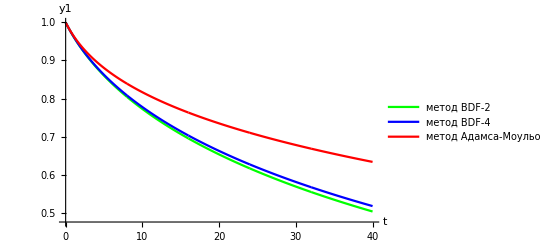

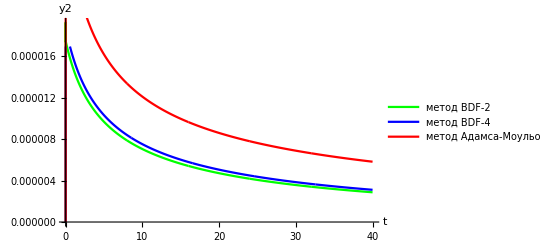

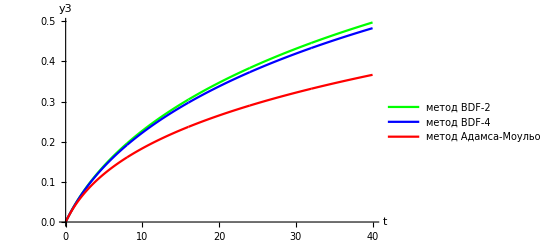

```mathematica
p0=Show[ListPlot3D[outMbdf2, PlotStyle->{Green}], ListPlot3D[outMbdf4, PlotStyle->{Blue}],ListPlot3D[outMimplicitAdams, PlotStyle->{Red}],AxesLabel->{"y1", "y2", "y3"}];

p1=Show[ListLinePlot[y1outMbdf2, PlotStyle->{Green}], ListLinePlot[y1outMbdf4, PlotStyle->{Blue}],ListLinePlot[y1outMimplicitAdams, PlotStyle->{Red}],AxesLabel->{"t", "y1"}];

p2=Show[ListLinePlot[y2outMbdf2, PlotStyle->{Green}], ListLinePlot[y2outMbdf4, PlotStyle->{Blue}],ListLinePlot[y2outMimplicitAdams, PlotStyle->{Red}],AxesLabel->{"t", "y2"}];

p3 = Show[ListLinePlot[y3outMbdf2, PlotStyle->{Green}], ListLinePlot[y3outMbdf4, PlotStyle->{Blue}],ListLinePlot[y3outMimplicitAdams, PlotStyle->{Red}],AxesLabel->{"t", "y3"}];

Legended[p0,LineLegend[{Green,Blue, Red},{"метод BDF-2","метод BDF-4", "метод Адамса-Моульона"}]]
Legended[p1,LineLegend[{Green,Blue, Red},{"метод BDF-2","метод BDF-4", "метод Адамса-Моульона"}]]
Legended[p2,LineLegend[{Green,Blue, Red},{"метод BDF-2","метод BDF-4", "метод Адамса-Моульона"}]]
Legended[p3,LineLegend[{Green,Blue, Red},{"метод BDF-2","метод BDF-4", "метод Адамса-Моульона"}]]
```

```mathematica
(*maxDiffAdams = 0;
maxDiffBDF2 = 0;
maxDiffBDF4 = 0;
For[i=1, i< Length[outMbdf2],++i, 
For[j = 1, j < Length[outMbdf2[[1]]], ++j,
(*maxDiffBDF2 =Max[Max[Abs [outMbdf2[[i]][[j]] - outMbdf4[[i]][[j]]],maxDiffAdams], Max[Abs [outMbdf2[[i]][[j]] - outMimplicitAdams[[i]][[j]]],maxDiffAdams]];*)
maxDiffBDF4 =Max[Abs [outMbdf4[[i]][[j]] - outMbdf2[[i]][[j]]],maxDiffAdams];
(*maxDiffAdams =Max[Max[Abs [outMimplicitAdams[[i]][[j]] - outMbdf2[[i]][[j]]],maxDiffAdams], Max[Abs [outMimplicitAdams[[i]][[j]] - maxDiffBDF4[[i]][[j]]],maxDiffAdams]];*)
]
]*)
```